```mathematica
SetDirectory["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\Funciones_dielectricas"]
```

C:\Users\Nanoplasmonics\Documents\GitHub\Tesis-de-Licenciatura\Funciones_dielectricas

```mathematica
h=6.62607015*10^(-34);
econst=1.602176634*10^(-19);
```

```mathematica
epsDrude[w_,wp_,g_]:=1-(wp^2)/(w*(w+I g));
```

```mathematica
epsPlata[w_]:=epsDrude[w,9,0.204]
```

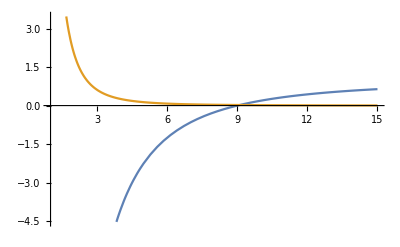

```mathematica
Plot[{Re[epsPlata[w]],Im[epsPlata[w]]},{w,1,15}]
```

```mathematica
epsPlataData=Table[{w*econst/h,Re[epsPlata[w]],Im[epsPlata[w]]},{w,1,15,0.01}];
```

```mathematica
Export["epsPlataData.csv",epsPlataData]
```

epsPlataData.csv